```mathematica
F[x_]:=1/2 ⅈ (PolyLog[2,-ⅈ ⅇ^x]-PolyLog[2,ⅈ ⅇ^x])
```

```mathematica
G3[a_,b_]:=F[a-b]+F[b-a]-π/2(a+b);
```

```mathematica
EnergySetup[n_,FacesCW_]:=Module[{i,rhoV,rhoF,include,LineFaces,f,Faces,NM,nonlinefaces,radii,RADII},
Faces=Sort/@FacesCW;
f=Length[Faces];
LineFaces={};rhoV=Table[Subscript[rV, i],{i,1,n-2}];rhoF=Table[Subscript[rF, i],{i,1,f-2}];
include = {};
nonlinefaces={};
For[i=1,i≤f,i++,
If[!(Faces[[i,-2]]==n-1&&Faces[[i,-1]]==n),
(* then *) AppendTo[include,i];AppendTo[nonlinefaces,FacesCW[[i]]],
(* else *) AppendTo[LineFaces,i]]];

NM=NMinimize[{∑_(k=1)^(f-2) ∑_(i=1)^Length[Faces[[include[[k]]]]] If[Faces[[include[[k]],i]]<n-1,G3[Subscript[rV, Faces[[include[[k]],i]]],Subscript[rF, k]],0]+∑_(i=1)^(n-2) Subscript[rV, i] π If[MemberQ[Flatten@Table[Faces[[LineFaces[[m]]]],{m,1,2}],i],(* then *) 1,(* else *) 2]+∑_(j=1)^(f-2) Subscript[rF, j] π If[MemberQ[Faces[[include[[j]]]],n-1]||MemberQ[Faces[[include[[j]]]],n],(* then *) 1,(* else *) 2],
∑_(i=1)^(n-2) Subscript[rV, i]+∑_(j=1)^(f-2) Subscript[rF, j]==0},Join[rhoV,rhoF]];
RADII=Exp[Re[Join[rhoV,rhoF]/.(NM[[2]])]];
RADII/=RADII[[1]];
radii=<||>;
For[i=1,i≤n-2,i++,
radii[i]=RADII[[i]]
];
For[i=1,i≤Length[nonlinefaces],i++,
radii[nonlinefaces[[i]]]=RADII[[n-2+i]]
];
{radii,LineFaces}
];
```

```mathematica
Boundary[n_,FacesCW_,LineFaces_,radii_,ϵ_:0]:=Module[{i,j,faces,vertices,lastvisited,d,h,H,breaker,unvisited,f,endcircle,ComputeEndcircle,ComputeEndcircle2,delete},
unvisited =FacesCW;(*Keeps track of the faces we haven't visited*)
f=Length[FacesCW];

faces=<||>; (* centers of face circles (or normals, for lines) *)
For[i=1,i≤f,i++,faces[FacesCW[[i]]]={-∞,-∞}];
vertices=<||>; (* centers of vertex circles (or normals, for lines) *)
For[i=1,i≤n-2,i++,vertices[i]={-∞,-∞}];
(* Radii is an assoc from v->rad and facelist->rad *)

(*Vertex circles going vertically upwards along first FaceLine*)
h=0; (* height along the left line *)
For[i=1,i≤Length[FacesCW[[LineFaces[[1]]]]]-2(*Number of vertex circles that lie along first LineFace*),i++,
vertices[FacesCW[[LineFaces[[1]],i]]]={0,h+radii[FacesCW[[LineFaces[[1]],i]]]};(*Set the center of this vertex circle*)
h+=2radii[[FacesCW[[LineFaces[[1]],i]]]]];(*Keeps track of our cumulative height as we climb up the first FaceLine*)

unvisited=Delete[unvisited,Position[unvisited,FacesCW[[LineFaces[[1]]]]]];

d=0;(*Horizontal distance*)

ComputeEndcircle[prev_,face_]:=
(*Returns which vertex circle we calculated last based on previous vertex circle and face*)
If[face[[Mod[Position[face,n-1][[1,1]]-2,Length[face]]+1]]==prev,
(*then*)face[[Mod[Position[face,n-1][[1,1]],Length[face]]+1]],
(*else*) face[[Mod[Position[face,n-1][[1,1]]-2,Length[face]]+1]]];

endcircle=ComputeEndcircle[n,FacesCW[[LineFaces[[1]]]]];(*Previous vertex circle is bottom line, face is first FaceLine*)

(*Face circles going horizontally across upper vertex line*)
breaker=True;
For[j=1,j≤f ,j++,
For[i=1,i≤Length[unvisited],i++,
If[MemberQ[unvisited[[i]],n-1], (*determine if this face-circle contains n-1, so it is on the upper vertex line*)
If[MemberQ[unvisited[[i]],ComputeEndcircle[endcircle,unvisited[[i]]]],
(*determine if this face-circle also contains the vertex right before n-1 to ensure we are going horizontally across in the right order*)
If[unvisited[[i]]==FacesCW[[LineFaces[[2]]]],
(* If we've reached the second faceline, then do nothing--find the other face circle containing endcircle*)
,
(* else if the face circle is not a line*)
faces[unvisited[[i]]]={d+radii[unvisited[[i]]],h}; (*Set the center of this face circle*)
d+=2radii[unvisited[[i]]]; (* update how far along the top line we are *)
endcircle=ComputeEndcircle[endcircle,unvisited[[i]]];(*Update endcircle*)
unvisited=Delete[unvisited,i];] (* remove that face from the unvisited list *)
]
]
]
];
(*Vertex circles along the second FaceLine, climbing vertically upwards*)
h=0;
For[i=1,i≤Length[FacesCW[[LineFaces[[2]]]]]-2,i++,
vertices[FacesCW[[LineFaces[[2]],i]]]={d,h+radii[FacesCW[[LineFaces[[2]],i]]]};h+=2radii[[FacesCW[[LineFaces[[2]],i]]]]];
H=h;
h=0;(*Reset height*)

ComputeEndcircle2[prev_,face_]:=
If[face[[Mod[Position[face,n][[1,1]]-2,Length[face]]+1]]==prev,
(*then*)face[[Mod[Position[face,n][[1,1]],Length[face]]+1]],
(*else*) face[[Mod[Position[face,n][[1,1]]-2,Length[face]]+1]]];

endcircle=ComputeEndcircle2[n-1,FacesCW[[LineFaces[[1]]]]];
(*Face circles along lower vertex line, moving horizontally from origin to second FaceLine*)
d=0;(*Reset distance*)
breaker=True;
For[j=1,j≤f,j++,
For[i=1,i≤Length[unvisited],i++,
If[MemberQ[unvisited[[i]],n], (* determine if this face-circle contains n *)
If[MemberQ[unvisited[[i]],endcircle(* ComputeEndcircle2[endcircle,unvisited[[i]]] *)],(* determine if this face-cirlce also contains the vertex right before n *)
If[unvisited[[i]]==FacesCW[[LineFaces[[2]]]],
(* If we've reached the second faceline, then do nothing*)
,
(* else *)
faces[unvisited[[i]]]={d+radii[unvisited[[i]]],h}; (* then we'll make this face's center be where we know it is *)
d+=2radii[unvisited[[i]]]; (* update how far along the bottom line we are *)
endcircle=ComputeEndcircle2[endcircle,unvisited[[i]]];
unvisited=Delete[unvisited,i];] (* remove that face from the unvisited list *)
]
]
]
];
(*Set the normals of the vertex lines and face lines*)
faces[FacesCW[[LineFaces[[2]]]]]={1,0};
faces[FacesCW[[LineFaces[[1]]]]]={-1,0};
vertices[n]={0,-1};
vertices[n-1]={0,1};

If[ThrowOrderError[faces,vertices,radii,d,H,n,FacesCW[[LineFaces]],0],
faces[FacesCW[[LineFaces[[1]]]]]*=-1;
faces[FacesCW[[LineFaces[[2]]]]]*=-1;
For[i=1,i≤n,i++,
If[i==n-1||i==n,
,
If[Abs[vertices[i][[1]]-d]≤ϵ,
vertices[i]={0,vertices[i][[2]]},
If[Abs[vertices[i][[1]]-0]≤ϵ,
vertices[i]={d,vertices[i][[2]]}]];
]]];

(*Return the assoc's of the faces to their centers and vertices to their centers*)
{vertices,faces,d,H}
];
```

```mathematica
FindRest[{x_,y_},r_,face_,vertices_,radii_,lines_]:=(* face is all the vertices that the face intersects *)
(*{x_,y_},r: known center of opposite kind and its radius
face: all the circles of its kind that pass thru that opposite known circle
vertices: all the circles of its kind that are tangent to the one we'e looking for*)
Module[{verts=vertices,i,j,ϕ,θ,ω,face2=face,b,b2=True},

If[verts[face2[[1]]]=={-∞,-∞}||MemberQ[lines,face2[[1]]],
For[i=2,i≤Length[face2]&&b2,i++,
If[verts[face2[[i]]]≠{-∞,-∞}&&!MemberQ[lines,face2[[i]]],
face2=Join[face2[[i;;]],face2[[;;i-1]]];
b2=False;
]]];

b=True;
For[i=2,i≤Length[face2]&&b,i++,
If[MemberQ[lines,face2[[i]]],
AppendTo[face2,face2[[1]]];
For[j=Length[face2]-1,j>i,j--,
If[verts[face2[[j]]]=={-∞,-∞},
ϕ=ArcTan[verts[face2[[j+1]]][[1]]-x,verts[face2[[j+1]]][[2]]-y];
θ=ArcTan[radii[face2[[j+1]]]/r];(* j+1 refers to previously computed / known *)
ω=ArcTan[radii[face2[[j]]]/r];
verts[face2[[j]]]={x+√(r^2+radii[face2[[j]]]^2)Cos[ϕ-θ-ω],y+√(r^2+radii[face2[[j]]]^2)Sin[ϕ-θ-ω]}
]
];b=False;Break,
If[verts[face2[[i]]]=={-∞,-∞},
ϕ=ArcTan[verts[face2[[i-1]]][[1]]-x,verts[face2[[i-1]]][[2]]-y];
θ=ArcTan[radii[face2[[i-1]]]/r];(* i-1 refers to previously computed / known *)
ω=ArcTan[radii[face2[[i]]]/r];
verts[face2[[i]]]={x+√(r^2+radii[face2[[i]]]^2)Cos[ϕ+θ+ω],y+√(r^2+radii[face2[[i]]]^2)Sin[ϕ+θ+ω]}];
];];
verts
];
```

```mathematica
Cull[assoc_]:=Module[{vis={},unv={},i},For[i=1,i≤Length[Keys[assoc]],i++,If[assoc[Keys[assoc][[i]]]=={-∞,-∞},AppendTo[unv,Keys[assoc][[i]]],AppendTo[vis,Keys[assoc][[i]]]]];{vis,unv}]
```

```mathematica
Interior[n_,FacesCW_,LineFaces_,radii_,vertices_,faces_,d_,h_]:=
Module[{Vunv={},Funv={},Vvis={},Fvis={},i,j,f,verts=vertices,verts2,fcs=faces,fcs2,fi,vi,x,y,k,b},
f=Length[FacesCW];
For[i=1,i≤n,i++,
If[vertices[i]=={-∞,-∞},AppendTo[Vunv,i],AppendTo[Vvis,i]]];
For[i=1,i≤f,i++,
If[faces[FacesCW[[i]]]=={-∞,-∞},AppendTo[Funv,FacesCW[[i]]],AppendTo[Fvis,FacesCW[[i]]]]];

For[j=1,j≤n+Length[FacesCW]&&(Length[Vunv]+Length[Funv]>0),j++,

For[i=1,i≤Length[Fvis],i++,(* for a known face circle *)
If[Length[Intersection[Vvis,Fvis[[i]]]]*Length[Intersection[Vunv,Fvis[[i]]]]>0,
fi=Fvis[[i]];
{x,y}=fcs[fi];
verts2=FindRest[{x,y},radii[fi],fi,verts,radii,{n-1,n}];
If[ThrowOrderError[fcs,verts2,radii,d,h,n,{FacesCW[[LineFaces[[1]]]],FacesCW[[LineFaces[[2]]]]},0],verts=FindRest[{x,y},radii[fi],Reverse[fi],verts,radii,{n-1,n}],
verts=verts2];
];
{Vvis,Vunv}=Cull[verts];
];

For[i=1,i≤Length[Vvis],i++, (* for a known vertex circle *)
If[b=False;
For[k=1,k≤Length[Fvis],k++,b=b||If[MemberQ[Fvis[[k]],Vvis[[i]]],True,False]];b,
If[b=False;For[k=1,k≤Length[Funv],k++,b=b||If[MemberQ[Funv[[k]],Vvis[[i]]],True,False]];b,
(* then *)
vi=Vvis[[i]];
{x,y}=verts[vi];
fcs2=FindRest[{x,y},radii[vi],FacesList[vi,FacesCW],fcs,radii,FacesCW[[LineFaces]]];
If[ThrowOrderError[fcs2,verts,radii,d,h,n,FacesCW[[LineFaces]],0],
fcs=FindRest[{x,y},radii[vi],
Reverse[FacesList[vi,FacesCW]],fcs,radii,FacesCW[[LineFaces]]],
fcs=fcs2];
];
{Fvis,Funv}=Cull[fcs];
]
];
];
{verts,fcs}
];
```

```mathematica
ThrowOrderError[fcs2_,verts_,radii_,d_,h_,n_,fls_,ϵ_](* fcs2 is proposed fcs association. fls is facelines *):=
Module[{i,j,b,b2,K},
K={};
For[i=1,i≤Length[Keys[fcs2]],i++,
If[!MemberQ[fls,Keys[fcs2][[i]]],AppendTo[K,Keys[fcs2][[i]]]]
];

b=False; (* "breaker" *)
For[i=1,i≤Length[K]&&!b,i++,
If[b2=False;
-∞<fcs2[K[[i]]][[1]]<0
||-∞<fcs2[K[[i]]][[2]]<0
||fcs2[K[[i]]][[1]]>d
||fcs2[K[[i]]][[2]]>h
||(For[j=1,j≤Length[K[[i]]],j++,
If[K[[i,j]]≠n-1&&K[[i,j]]≠n&&verts[K[[i,j]]]≠{-∞,-∞}&&fcs2[K[[i]]]≠{-∞,-∞},
If[EuclideanDistance[verts[K[[i,j]]],fcs2[K[[i]]]]≥(1-ϵ)(radii[K[[i,j]]]+radii[K[[i]]]),b2=True;Break]]];b2),
b=True,

For[j=1,j≤Length[K]&&!b,j++,
If[i≠j&&fcs2[K[[i]]]≠{-∞,-∞}&&fcs2[K[[j]]]≠{-∞,-∞}&&
EuclideanDistance[fcs2[K[[i]]],fcs2[K[[j]]]]<(1+ϵ)(radii[fcs2[K[[i]]]]+radii[fcs2[K[[j]]]])
,(* then, bad *) b=True]]];
];


For[i=1,i≤Length[fls[[1]]]&&!b,i++,
If[verts[fls[[1,i]]][[1]]≠d/2+fcs2[fls[[1]]][[1]] d/2&&fls[[1,i]]<n-1,b=True]
];
For[i=1,i≤Length[fls[[2]]]&&!b,i++,
If[verts[fls[[2,i]]][[1]]≠d/2+fcs2[fls[[2]]][[1]] d/2&&fls[[2,i]]<n-1,b=True]
];

b
];
```

```mathematica
FacesList[v_,Faces_]:=
Module[{ContainV={},i,L=2,p=3,temp},
For[i=1,i≤Length[Faces],i++,
If[MemberQ[Faces[[i]],v],AppendTo[ContainV,Faces[[i]]]]];
While[L<Length[ContainV],
While[p≤Length[ContainV],
If[Length[Intersection[ContainV[[L-1]],ContainV[[p]]]]==2,
temp=ContainV[[p]];ContainV[[p]]=ContainV[[L]];ContainV[[L]]=temp;p=1+Length[ContainV],
p++]
];
L++;
p=L+1;
];
ContainV];
```

```mathematica
Q=({{0, 1/2, 0, 0}, {1/2, 0, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
```

```mathematica
InvCoords[z_,r_,d_:0]:=If[r==∞,{2d,0,z},{Norm[z]^2/r-r,1/r,z/r}];
```

```mathematica
Gram[SC_]:=SC.Q.Transpose[SC];
SuperCluster[vertices_,faces_,radii_,fls_,d_,h_,n_]:=
Module[{sc={},i},
For[i=1,i≤n-2,i++,AppendTo[sc,Flatten[InvCoords[vertices[i],radii[i]]]]];
AppendTo[sc,Flatten[InvCoords[vertices[n-1],∞,h/2+vertices[n-1][[2]] h/2]]];
AppendTo[sc,Flatten[InvCoords[vertices[n],∞,h/2+vertices[n][[2]] h/2]]];
For[i=1,i≤Length[Keys[faces]],i++,
If[!MemberQ[fls,Keys[faces][[i]]],
AppendTo[sc,Flatten[InvCoords[faces[Keys[faces][[i]]],radii[Keys[faces][[i]]]]]]
]];
AppendTo[sc,Flatten[InvCoords[faces[fls[[1]]],∞,d/2+faces[fls[[1]]][[1]] d/2]]];
AppendTo[sc,Flatten[InvCoords[faces[fls[[2]]],∞,d/2+faces[fls[[2]]][[1]] d/2]]];
sc
];
```

```mathematica
DrawCircle[{bhat_,b_,bx_,by_}]:=If[Abs[b]≥ .01,Circle[{bx,by}/b,1/b],InfiniteLine[{bx,by}bhat/2,{-by,bx}]];
```

```mathematica
Packing[n_,FacesCW_,ϵ_:0]:=
Module[{radii,LineFaces,vertices,faces,d,h},
{radii,LineFaces}=EnergySetup[n,FacesCW];
{vertices,faces,d,h}=Boundary[n,FacesCW,LineFaces,radii,ϵ];
{vertices,faces}=Interior[n,FacesCW,LineFaces,radii,vertices,faces,d,h];
{vertices,faces,radii,d,h,LineFaces}];
```

```mathematica
Render[radii_,fcs_,verts_,fls_,n_,d_,h_]:=Graphics[{Blue,Thick,
Table[If[i==n-1,Line[{{-Max[Values[radii]],h},{d+Max[Values[radii]],h}}],If[i==n,Line[{{-Max[Values[radii]],0},{d+Max[Values[radii]],0}}],
Circle[verts[Keys[verts][[i]]],radii[Keys[verts][[i]]]]]],{i,1,n}],
Red,Dashed,
Table[If[Keys[fcs][[i]]==fls[[1]],Line[{{0,-Max[Values[radii]]},{0,h+Max[Values[radii]]}}],
If[Keys[fcs][[i]]==fls[[2]],Line[{{d,-Max[Values[radii]]},{d,h+Max[Values[radii]]}}],
Circle[fcs[Keys[fcs][[i]]],radii[Keys[fcs][[i]]]]]],{i,1,Length[Keys[fcs]]}]
}];
```

```mathematica
SendToInt[ϵ_:0][y_]:=With[{x=Simplify[y]},If[Abs[x-Floor[x]]≤ϵ ,Floor[x],
If[Abs[x-Ceiling[x]]≤ ϵ ,Ceiling[x],x],x]];
```

```mathematica
R[vhat_]:=IdentityMatrix[4]+2Q.Transpose[{vhat}].{vhat}
BMat[n_]:=Table[b[i,j],{i,1,n},{j,1,n}];

Bend[V_,m_][i_]:=
Module[{sol,assignments,rest,l,others1,others2},
sol=Solve[BMat[m].(V[[;;m]])==(V[[;;m]]).R[V[[m+i]]]][[1]];
assignments=Association[sol];
rest=Complement[Flatten[BMat[m]],Keys[assignments]];
l=Length[rest];
others1=Solve[rest==Table[0,{j,1,l}]][[1]];
others2=<||>;
For[j=1,j≤l,j++,others2[rest[[j]]]=Subscript[a, j]];
others2=Normal[others2];
Column[{
MatrixForm[(BMat[m]/.assignments)/.others2],
MatrixForm[(BMat[m]/.assignments)/.others1]
}]
];
```

```mathematica
Everything[n_,FacesCW_,ϵ_:0,steps_,sizemax_:∞]:=Module[{vertices,faces,f=Length[FacesCW],radii,d,h,LineFaces,Vnye,Vout,bends={}},
{vertices,faces,radii,d,h,LineFaces}=Packing[n,FacesCW,ϵ];
Vnye=SendToInt[ϵ]//@SuperCluster[vertices,faces,radii,FacesCW[[LineFaces]],d,h,n];
Vout=MatrixForm[Simplify[RootApproximant[Vnye]]];
bends=Bend[Vout[[1]],n]/@Range@f;
Column[{
Render[radii,faces,vertices,FacesCW[[LineFaces]],n,d,h],
Graphics[{Thick, DrawCircle/@Orbit[Vnye[[-f;;]],Vnye[[;;n]],steps,sizemax],Red,DrawCircle/@Vnye[[-f;;]], Blue, DrawCircle/@Vnye[[;;n]]},PlotRange->{{-d,2 d},{-1.2 Max[Values[radii]],h+1.2 Max[Values[radii]]}},PlotRangeClipping->True],
Vout,
bends,
MatrixForm[Simplify[RootApproximant[
SendToInt[ϵ]//@Gram[SuperCluster[vertices,faces,radii,FacesCW[[LineFaces]],d,h,n]]]
]]
}]]
```

```mathematica
Orbit[co_,cl_,steps_,sizemax_:∞]:=Module[{i,j,k,orbit=cl,L},
For[i=1,i≤steps,i++,
L=Length[orbit];
For[j=1,j≤Length[co],j++,
For[k=1,k≤L,k++,
If[(orbit⟦k⟧.R[co⟦j⟧])⟦2⟧≤sizemax&&!MemberQ[Round[N[orbit],.001],Round[N[orbit⟦k⟧.R[co⟦j⟧]],.001](*new thing*)],AppendTo[orbit,orbit⟦k⟧.R[co⟦j⟧](*newthing*)]]
]
]
];
orbit
];
```

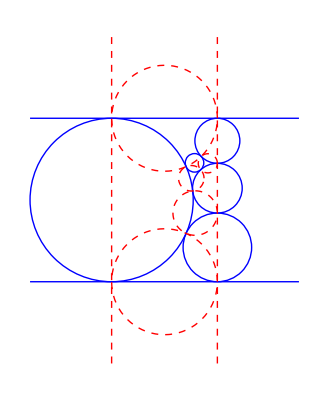
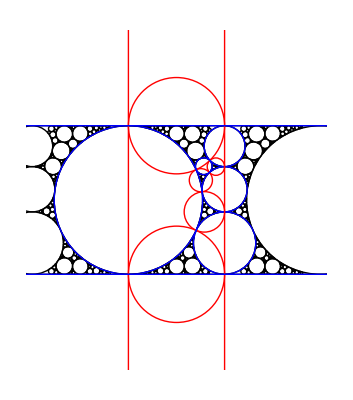
-Graphics-
-Graphics-
(1/58 (6919+√52292973) | 1 | Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] | Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2]
0 | Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] | 0 | 1
Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] | Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] | Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | 1
Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] | Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2] | Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3] | Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2]
Root[472+476 #1-443 #1^2+3 #1^3&,3] | Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1] | Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4] | Root[-1-10 #1-6 #1^3+#1^4&,2]
Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] | 0 | 0 | 1
0 | 0 | 0 | -1
1/25 (3362+16 √39599) | Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2] | Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] | Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]
Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] | Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] | 1 | Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]
0 | Root[-3+16 #1+7 #1^2-2 #1^3-2 #1^4-3 #1^5+8 #1^6-#1^7-3 #1^8+10 #1^9+9 #1^10&,2] | 1 | 0
1/380 (27209+√738938881) | Root[-1+#1-#1^3+2 #1^4-#1^6+#1^8+3 #1^9-2 #1^10+2 #1^11+#1^12&,2] | Root[-1-10 #1-6 #1^3+#1^4&,2] | Root[-28+71 #1-83 #1^2+38 #1^4-37 #1^5+4 #1^6&,2]
Root[1554+97 #1-1853 #1^2+34 #1^3&,3] | Root[-1+3 #1-#1^2-#1^4-2 #1^5-3 #1^6-#1^7-4 #1^8+4 #1^9-4 #1^10-3 #1^11+3 #1^12+#1^13&,3] | Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] | Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]
0 | 0 | -1 | 0
Root[31-81 #1+6 #1^2+37 #1^3+70 #1^4-26 #1^5+#1^6&,4] | 0 | 1 | 0)
{(a_1 | -(194996 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+928 √39599 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]-2900 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+1450 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]-2900 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]-1450 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+172975 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+25 √52292973 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-194996 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-928 √39599 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+2900 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+2900 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-172975 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2-25 √52292973 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2)/(1450 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-((-Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]+Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_1)/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-((-Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]+Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_2)/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-((-Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]+Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_3)/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) | -(-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]+2 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]-1/58 (6919+√52292973) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] a_1)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3] a_2)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4] a_3)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | a_2 | a_3 | -(4874900 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+23200 √39599 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-72500 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+36250 Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-72500 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2 Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-1247866879 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-6239872 √39599 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-625 √52292973 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+9749800 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+46400 √39599 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+9749800 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+46400 √39599 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+4324375 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+625 √52292973 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-581541950 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-2767600 √39599 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-84050 √52292973 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-400 √2070749437827 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/(36250 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-((-58 Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+6919 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+√52292973 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_1)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-((-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]+Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_2)/(Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-((-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]+Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_3)/(Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) | -(4874900 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+23200 √39599 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-72500 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+36250 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-72500 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-1247866879 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-6239872 √39599 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-625 √52292973 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+9749800 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+46400 √39599 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+9749800 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+46400 √39599 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-36250 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+36250 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+4874900 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+23200 √39599 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-72500 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]^2 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-72500 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+4324375 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+625 √52292973 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-581541950 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-2767600 √39599 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-84050 √52292973 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-400 √2070749437827 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-4874900 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-23200 √39599 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+72500 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+4324375 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+625 √52292973 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+72500 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-4324375 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2-625 √52292973 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2)/(36250 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-((-58 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+6919 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+√52292973 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-58 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_1)/(58 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-((-Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]+Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_2)/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-((-Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]+Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-Root[-1-10 #1-6 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_3)/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])
a_4 | (Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(2 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_4-(Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_5-(Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_6 | -(-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] a_4)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3] a_5)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4] a_6)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | a_5 | a_6 | -(-1/625 (3362+16 √39599)^2 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2/25 (3362+16 √39599) Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+(-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-((6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_4-(Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_5-(Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_6 | 1/25 (-25-3362 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-16 √39599 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+50 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]^2)-(-1/625 (3362+16 √39599)^2 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2/25 (3362+16 √39599) Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(2 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(-Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2]+1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_4-(-Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2]+Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_5-(-Root[-1-10 #1-6 #1^3+#1^4&,2]+Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_6
a_7 | (Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(2 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2-Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_7-(Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_8-(Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_9 | -(-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] a_7)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3] a_8)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4] a_9)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | a_8 | a_9 | (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(-1/625 (3362+16 √39599)^2 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2/25 (3362+16 √39599) Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+2/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-((6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_7-(Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_8-(Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_9 | (Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])+1/25 (-25-3362 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-16 √39599 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+50 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]^2+50 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-25 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])-(2 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2-Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(-1/625 (3362+16 √39599)^2 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2/25 (3362+16 √39599) Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+2/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(-Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2]+1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_7-(-Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2]+Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_8-(-Root[-1-10 #1-6 #1^3+#1^4&,2]+Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_9
a_10 | (Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2-Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_10-(Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_11-(Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_12 | -(-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] a_10)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3] a_11)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4] a_12)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | a_11 | a_12 | (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(-1/625 (3362+16 √39599)^2 Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2/25 (3362+16 √39599) Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+2/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-((6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_10-(Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_11-(Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_12 | (Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])+1/25 (-25 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2]-3362 Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-16 √39599 Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+50 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]^2+50 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]-25 Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])-(-1/625 (3362+16 √39599)^2 Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2/25 (3362+16 √39599) Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+2/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2-Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(-Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2]+1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_10-(-Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2]+Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_11-(-Root[-1-10 #1-6 #1^3+#1^4&,2]+Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_12
a_13 | (Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-1-10 #1-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(2 Root[-1-10 #1-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2-Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_13-(Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_14-(Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_15 | -(-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-1-10 #1-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] a_13)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3] a_14)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4] a_15)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | a_14 | a_15 | (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-1-10 #1-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(-1/625 (3362+16 √39599)^2 Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]+2/25 (3362+16 √39599) Root[-1-10 #1-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+2/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]-Root[472+476 #1-443 #1^2+3 #1^3&,3] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-((6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_13-(Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_14-(Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_15 | (Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-1-10 #1-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])+1/25 (-25 Root[-1-10 #1-6 #1^3+#1^4&,2]-3362 Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-16 √39599 Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+50 Root[-1-10 #1-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]^2+50 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]-25 Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])-(-1/625 (3362+16 √39599)^2 Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]+2/25 (3362+16 √39599) Root[-1-10 #1-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+2/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]-Root[472+476 #1-443 #1^2+3 #1^3&,3] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(2 Root[-1-10 #1-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2-Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(-Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2]+1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_13-(-Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2]+Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_14-(-Root[-1-10 #1-6 #1^3+#1^4&,2]+Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_15
a_16 | (Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(2 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2)/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_16-(Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_17-(Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_18 | -(2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] a_16)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3] a_17)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4] a_18)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | a_17 | a_18 | (2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(2/25 (3362+16 √39599) Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-((6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_16-(Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_17-(Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_18 | -1+2 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]^2-Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(2 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2)/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(2/25 (3362+16 √39599) Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(-Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2]+1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_16-(-Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2]+Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_17-(-Root[-1-10 #1-6 #1^3+#1^4&,2]+Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_18
a_19 | -(2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])+(2 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_19-(Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_20-(Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_21 | (2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] a_19)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3] a_20)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4] a_21)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | a_20 | a_21 | (4 (1681+8 √39599) Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3])/(25 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-(2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-((6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_19-(Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_20-(Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_21 | 1-2 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]^2+(4 (1681+8 √39599) Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3])/(25 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-(2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])+(2 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(-Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2]+1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_19-(-Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2]+Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_20-(-Root[-1-10 #1-6 #1^3+#1^4&,2]+Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_21)
(0 | -(194996 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+928 √39599 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]-2900 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+1450 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]-2900 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]-1450 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+172975 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+25 √52292973 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-194996 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-928 √39599 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+2900 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+2900 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-172975 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2-25 √52292973 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2)/(1450 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) | -(-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]+2 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]-1/58 (6919+√52292973) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | 0 | 0 | -(4874900 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+23200 √39599 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-72500 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+36250 Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-72500 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2 Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-1247866879 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-6239872 √39599 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-625 √52292973 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+9749800 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+46400 √39599 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+9749800 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+46400 √39599 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+4324375 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+625 √52292973 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-581541950 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-2767600 √39599 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-84050 √52292973 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-400 √2070749437827 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/(36250 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) | -(4874900 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+23200 √39599 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-72500 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+36250 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-72500 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-1247866879 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-6239872 √39599 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-625 √52292973 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+9749800 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+46400 √39599 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+9749800 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+46400 √39599 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-36250 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+36250 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+4874900 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+23200 √39599 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-72500 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]^2 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-72500 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+4324375 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+625 √52292973 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-581541950 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-2767600 √39599 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-84050 √52292973 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-400 √2070749437827 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-4874900 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-23200 √39599 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+72500 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+4324375 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+625 √52292973 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+72500 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-4324375 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2-625 √52292973 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2)/(36250 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])
0 | (Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(2 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] | -(-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | 0 | 0 | -(-1/625 (3362+16 √39599)^2 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2/25 (3362+16 √39599) Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+(-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | 1/25 (-25-3362 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-16 √39599 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+50 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]^2)-(-1/625 (3362+16 √39599)^2 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2/25 (3362+16 √39599) Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(2 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]
0 | (Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(2 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2-Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] | -(-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | 0 | 0 | (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(-1/625 (3362+16 √39599)^2 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2/25 (3362+16 √39599) Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+2/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] | (Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])+1/25 (-25-3362 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-16 √39599 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+50 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]^2+50 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-25 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])-(2 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2-Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(-1/625 (3362+16 √39599)^2 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2/25 (3362+16 √39599) Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+2/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]
0 | (Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2-Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] | -(-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | 0 | 0 | (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(-1/625 (3362+16 √39599)^2 Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2/25 (3362+16 √39599) Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+2/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] | (Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])+1/25 (-25 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2]-3362 Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-16 √39599 Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+50 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]^2+50 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]-25 Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])-(-1/625 (3362+16 √39599)^2 Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2/25 (3362+16 √39599) Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+2/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2-Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]
0 | (Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-1-10 #1-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(2 Root[-1-10 #1-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2-Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] | -(-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-1-10 #1-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | 0 | 0 | (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-1-10 #1-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(-1/625 (3362+16 √39599)^2 Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]+2/25 (3362+16 √39599) Root[-1-10 #1-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+2/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]-Root[472+476 #1-443 #1^2+3 #1^3&,3] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] | (Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-1/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-1-10 #1-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-(1-2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2]^2) Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])+1/25 (-25 Root[-1-10 #1-6 #1^3+#1^4&,2]-3362 Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-16 √39599 Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+50 Root[-1-10 #1-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]^2+50 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]-25 Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])-(-1/625 (3362+16 √39599)^2 Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]+2/25 (3362+16 √39599) Root[-1-10 #1-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]+2/25 (3362+16 √39599) Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]-Root[472+476 #1-443 #1^2+3 #1^3&,3] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(2 Root[-1-10 #1-6 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2-Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]
0 | (Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(2 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2)/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] | -(2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | 0 | 0 | (2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(2/25 (3362+16 √39599) Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] | -1+2 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]^2-Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]+(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(2 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]^2)/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(2/25 (3362+16 √39599) Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] (1+1/25 (3362+16 √39599) Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2]))/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]
0 | -(2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])+(2 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] | (2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | 0 | 0 | (4 (1681+8 √39599) Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3])/(25 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-(2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | 1-2 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3]^2+(4 (1681+8 √39599) Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3])/(25 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-(2 Root[37+8 #1-22 #1^2-8 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])+(2 Root[62-37 #1+16 #1^2-7 #1^3-148 #1^4+12 #1^5&,3] Root[1+#1+#1^3+#1^6-3 #1^9-#1^10+#1^11-#1^12-2 #1^13+2 #1^15-#1^16+#1^17+#1^18-4 #1^19-#1^20+#1^21+#1^22+#1^23&,2])/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]),(a_1 | -(58 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]-58 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]-116 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]+6919 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+√52292973 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-58 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-58 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+116 Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+116 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-6919 Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]^2 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-√52292973 Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]^2 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])/(58 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-((-Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]+Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_1)/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-((-Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]+Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_2)/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-((-Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]+Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_3)/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) | -(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2]+Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]+2 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-1/58 (6919+√52292973) Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] a_1)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3] a_2)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4] a_3)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | a_2 | a_3 | -(58 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-58 Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-116 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]+6919 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+√52292973 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-6919 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-√52292973 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-58 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2]^2 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+116 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+116 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-6919 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-√52292973 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-((-58 Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+6919 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+√52292973 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_1)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-((-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]+Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_2)/(Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-((-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]+Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_3)/(Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) | -(58 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-58 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-116 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]+6919 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+√52292973 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-6919 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-√52292973 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-58 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2]^2 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+116 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+58 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+116 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+58 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-116 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-116 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]^2 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-6919 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-√52292973 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-58 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+116 Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+116 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+6919 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+√52292973 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-6919 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]^2 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-√52292973 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]^2 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])/(58 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-((-58 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+6919 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+√52292973 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-58 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_1)/(58 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-((-Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]+Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_2)/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-((-Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]+Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-Root[-1-10 #1-6 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_3)/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])
a_4 | 1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-(2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_4-(Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_5-(Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_6 | -(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] a_4)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3] a_5)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4] a_6)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | a_5 | a_6 | -(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2]^2 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-((6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_4-(Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_5-(Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_6 | -Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]^2-(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2]^2 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-(2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(-Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2]+1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_4-(-Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2]+Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_5-(-Root[-1-10 #1-6 #1^3+#1^4&,2]+Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_6
a_7 | (Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]^2-Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_7-(Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_8-(Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_9 | -(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] a_7)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3] a_8)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4] a_9)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | a_8 | a_9 | (-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2]^2 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-((6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_7-(Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_8-(Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_9 | -1-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]^2-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2]^2 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]^2-Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(-Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2]+1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_7-(-Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2]+Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_8-(-Root[-1-10 #1-6 #1^3+#1^4&,2]+Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_9
a_10 | -(2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]^2-Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_10-(Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_11-(Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_12 | -(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] a_10)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3] a_11)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4] a_12)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | a_11 | a_12 | -(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2]^2 Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-((6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_10-(Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_11-(Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_12 | -Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2]-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]+2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]^2-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]-(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2]^2 Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]^2-Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(-Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2]+1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_10-(-Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2]+Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_11-(-Root[-1-10 #1-6 #1^3+#1^4&,2]+Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_12
a_13 | -(2 Root[-1-10 #1-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]^2-Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]+2 Root[-1-10 #1-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_13-(Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_14-(Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_15 | -(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]+2 Root[-1-10 #1-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] a_13)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3] a_14)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4] a_15)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | a_14 | a_15 | -(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2]^2 Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]+2 Root[-1-10 #1-6 #1^3+#1^4&,2] Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[472+476 #1-443 #1^2+3 #1^3&,3] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]+2 Root[-1-10 #1-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-((6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_13-(Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_14-(Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_15 | -Root[-1-10 #1-6 #1^3+#1^4&,2]-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]+2 Root[-1-10 #1-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]^2-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]-(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2]^2 Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]+2 Root[-1-10 #1-6 #1^3+#1^4&,2] Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[472+476 #1-443 #1^2+3 #1^3&,3] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(2 Root[-1-10 #1-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]^2-Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]+2 Root[-1-10 #1-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(-Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2]+1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_13-(-Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2]+Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_14-(-Root[-1-10 #1-6 #1^3+#1^4&,2]+Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_15
a_16 | -(2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]^2)/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_16-(Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_17-(Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_18 | -(2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] a_16)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3] a_17)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4] a_18)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | a_17 | a_18 | 1-(2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+(2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-((6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_16-(Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_17-(Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_18 | -(2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]^2+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-(2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]^2)/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(-Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2]+1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_16-(-Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2]+Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_17-(-Root[-1-10 #1-6 #1^3+#1^4&,2]+Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_18
a_19 | (2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] (-Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_19-(Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_20-(Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_21 | (2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] a_19)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3] a_20)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4] a_21)/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | a_20 | a_21 | (2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-((6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_19-(Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_20-(Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) a_21 | 1+(2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]^2+(2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]-(2 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(-Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2]+1/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(6919+√52292973)/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4])-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_19-(-Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2]+Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_20-(-Root[-1-10 #1-6 #1^3+#1^4&,2]+Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+Root[472+476 #1-443 #1^2+3 #1^3&,3]/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])) a_21)
(0 | -(58 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]-58 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]-116 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]+6919 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+√52292973 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-58 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-58 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+116 Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+116 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-6919 Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]^2 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-√52292973 Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]^2 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])/(58 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) | -(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2]+Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2]+2 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-1/58 (6919+√52292973) Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | 0 | 0 | -(58 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-58 Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-116 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]+6919 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+√52292973 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-6919 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-√52292973 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-58 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2]^2 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+116 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+116 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-6919 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-√52292973 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])/(58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) | -(58 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-58 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-116 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]+6919 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+√52292973 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-6919 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-√52292973 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-58 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2]^2 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+116 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-58 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+58 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+116 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+58 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-116 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-116 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]^2 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-6919 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-√52292973 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-58 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+116 Root[30-207 #1-11 #1^2-43 #1^3-30 #1^4-14 #1^5+2 #1^6&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+116 Root[-17-54 #1-32 #1^2-10 #1^3+#1^4&,2] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+6919 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+√52292973 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-6919 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]^2 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-√52292973 Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]^2 Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])/(58 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])
0 | 1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-(2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) | -(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | 0 | 0 | -(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2]^2 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | -Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]^2-(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2]^2 Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-(2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])
0 | (Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]^2-Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] | -(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | 0 | 0 | (-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]-(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2]^2 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] | -1-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]^2-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]+(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])-(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2]^2 Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2]+2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]^2-Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]
0 | -(2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]^2-Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) | -(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | 0 | 0 | -(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2]^2 Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]+(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | -Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2]-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]+2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]^2-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+2 Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]-(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2]^2 Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^5+3 #1^6&,4]-(2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]^2-Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3])/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1-2 #1+24 #1^2-37 #1^3+17 #1^4&,2]+2 Root[-13-10 #1+12 #1^2-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[-682+92 #1-571 #1^2-833 #1^3+10 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[-4-#1-6 #1^2+3 #1^3+10 #1^4-3 #1^6-6 #1^7-5 #1^9-3 #1^10+#1^11&,3]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2])
0 | -(2 Root[-1-10 #1-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]^2-Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1]+(Root[1-9 #1+20 #1^2-6 #1^3+17 #1^4&,2] (-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]+2 Root[-1-10 #1-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4]))/(Root[1-8 #1-7 #1^2-4 #1^3+17 #1^4&,1] Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2]) | -(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]+2 Root[-1-10 #1-6 #1^3+#1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[472+476 #1-443 #1^2+3 #1^3&,3] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2]+Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/Root[5-4 #1+2 #1^2+2 #1^3-3 #1^5+#1^6+2 #1^7-2 #1^9-#1^10+#1^12+2 #1^13-#1^14-3 #1^15+#1^16&,2] | 0 | 0 | -(-Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2]^2 Root[1-#1-8 #1^2+4 #1^3+17 #1^4&,1]+2 Root[-1-10 #1-6 #1^3+#1^4&,2] Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2-5 #1+2 #1^2+2 #1^3+3 #1^5-6 #1^6-11 #1^7+#1^8+#1^9&,3]-Root[472+476 #1-443 #1^2+3 #1^3&,3] (1+Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-1+5 #1+4 #1^2+#1^3-3 #1^4+5 #1^5-12 #1^6+#1^7+11 #1^8-14 #1^9+9 #1^10&,2])+2 Root[-300-200 #1-261 #1^2-104 #1^3+2 #1^4&,2] Root[-2+3 #1+2 #1^2-4 #1^3-6 #1^4+6 #1^5-2 #1^6+7 #1^7+2 #1^8-#1^10+2 #1^11+#1^12-5 #1^13+#1^14&,4])/Root[2+122 #1+#1^2+130 #1^3-104 #1^4-103 #1^

```mathematica
Everything[7,{{1,4,5},{2,1,5,6},{3,2,7},{2,6,7},{1,2,4},{2,3,4},{3,4,5,6,7}},1/100,5,35]
```